# WELP Project Proposal: Functional Iterates and Roots

Note for WELP:U Students - as you are doing this project individually, you can simply ignore references to groups when filling this out.

#### Please save this notebook with the filename WELP24 Project Proposal - Group # (or - Name for WELP:U) and put it in the Project Proposal Submissions folder

## Proj-Group-6

Bertie Bennet

Christopher Gilbert

Gregory Roudenko

Mentor: Daniele Ceravolo

## Project Title: Exploring Functional Roots and Iteration

### The Problem

Given a function f(x), how do you find a function g(x) such that g(g(x)) = f(x)?
How can this be extended to find g^n(x) = f(x) for all natural numbers n?
Is it possible for n to be more than just a natural number (i.e. can it be negative, rational, irrational, and complex)?

### How you plan to solve it

We can first explore if it is possible to find functional roots for specific function types. For example, we’ve already found an explicit formula for any complex functional exponent z of a complex power function. Some other types of functions don’t have an algebraic closed form solution, such as exponentials, but we could still explore these functions by using other techniques.

### Why is this a good fit for you/your team?

We are all very experienced in high-level mathematics, and a lot of the project relies on being able to see patterns in functional iteration and using them to generalize formulas. Given that in one of our meetings, we managed to completely solve functional roots for power functions (first by finding a pattern to give a formula for repeated exponentiation, inverting that pattern to give functional roots, finding a formula for computing a summation which was needed for the inversion, generalizing to complex exponents, etc.), I would say that we are capable of making great progress on this problem.

### What data do you need?

evidence that you’ve found, imported and verified that you have usable data

As it’s much more of a mathematical problem, we shouldn’t need outside data to solve it.

### Do you have any code showing your project is viable?

#### Power Function Roots

```mathematica
(* for f(x) = a*b^x, find g(x)=f^M(x) *)
j[a_,b_,x_, M_]:=a^((1-b^M)/(1-b))*x^(b^M)
```

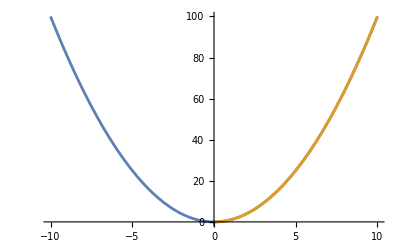

```mathematica
Plot[{1*x^2,j[1, 2, j[1, 2, x,1/2], 1/2]}, {x, -10, 10}]
```

```mathematica
ListLinePlot3D[Table[{x,Re[#],Im[#]}&[j[1,2,x,1+I]],{x,0,100,0.01}]]
```

-Graphics3D-

#### Numerical Solution

Idk why it’s giving errors, ask Gregory

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

{x→0,g[0]→0,g'[0]→1,g''[0]→0,g^(3)[0]→-1/2,g^(4)[0]→0,g^(5)[0]→-3/4,g^(6)[0]→0,g^(7)[0]→-53/8,g^(8)[0]→0,g^(9)[0]→-1863/16,g^(10)[0]→0,g^(11)[0]→-92713/32,g^(12)[0]→0,g^(13)[0]→-3710155/64,g^(14)[0]→0,g^(15)[0]→594673187/128,g^(16)[0]→0,g^(17)[0]→329366540401/256,g^(18)[0]→0,g^(19)[0]→104491760828591/512,g^(20)[0]→0}

Part::partw: Part 23 of {x→0,g[0]→0,g'[0]→1,g''[0]→0,g^(3)[0]→-1/2,g^(4)[0]→0,g^(5)[0]→-3/4,g^(6)[0]→0,g^(7)[0]→-53/8,g^(8)[0]→0,«12»} does not exist.

Part::partw: Part 24 of {x→0,g[0]→0,g'[0]→1,g''[0]→0,g^(3)[0]→-1/2,g^(4)[0]→0,g^(5)[0]→-3/4,g^(6)[0]→0,g^(7)[0]→-53/8,g^(8)[0]→0,«12»} does not exist.

Part::partw: Part 25 of {x→0,g[0]→0,g'[0]→1,g''[0]→0,g^(3)[0]→-1/2,g^(4)[0]→0,g^(5)[0]→-3/4,g^(6)[0]→0,g^(7)[0]→-53/8,g^(8)[0]→0,«12»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

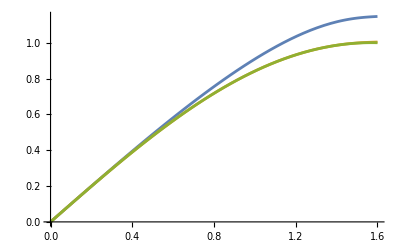

```mathematica
f[x_]:=g[g[x]];
values={x->0,g[0]->0};
original[x_]=Sin[x];

Table[values=Append[values,First[Last[Solve[(D[f[x],{x,i}]//.{values})==(D[original[x],{x,i}]/. {x->0})]]]];,{i,Range[1,20]}]
values
fun=Sum[Last[values[[n+2]]]*(x^n)/n!,{n,0,40}];
thing[a_]:=fun/. {x->a}
Plot[{thing[m],thing[thing[m]],Sin[m]},{m,0,1.6}]
```

## Planning

### When will you meet with your group? How often? For how long?

Weekly on Wednesdays at 8:00 PM EST for two hours

### Where are you keeping your task list?

link to Trello-type board

https://trello.com/invite/b/66f6a5152acce6587fb60de7/ATTI3fede8c49ed3bb873e8226e75df67907903794C0/welp-functional-iterates

### Outline your Sprints (recommended 3-6)

#### Sprint 1

Dates

Goals

How will you judge if you’ve accomplished the goals?

Who is responsible for what?

#### Sprint 2

#### Sprint 3

#### Sprint 4

#### Sprint 5

#### Sprint 6